A[1] = 0  B[1] = 0

A[2] = 4/(3 π)  B[2] = 0

A[3] = 0  B[3] = 0

A[4] = -4/(15 π)  B[4] = 0

{2/π+(4 Cos[2 t])/(3 π)-(4 Cos[4 t])/(15 π),2/π+(4 Cos[2 t])/(3 π)-(4 Cos[4 t])/(15 π)}

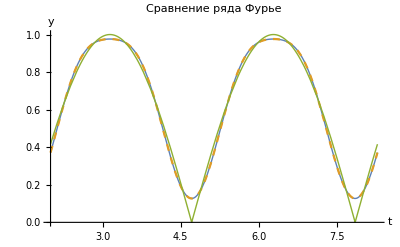

2/π+(4 Cos[2 t])/(3 π)-(4 Cos[4 t])/(15 π)

2/π+(4 Cos[2 t])/(3 π)-(4 Cos[4 t])/(15 π)

```mathematica
f2[t_]:=Abs[Cos[t]]


n=4;
h=2;
T=2 Pi;

p=FourierTrigSeries[f2[t],t,n];

nCorrected=If[EvenQ[n],n+1,n];

A[i_]:=(2/T) Integrate[f2[t] Cos[(2 Pi i t)/T],{t,h,h+T}];
B[i_]:=(2/T) Integrate[f2[t] Sin[(2 Pi i t)/T],{t,h,h+T}];

(*Ряд Фурье вручную*)
rad=A[0]/2;
For[i=1,i<nCorrected,i++,Print["A[",i,"] = ",A[i],"  B[",i,"] = ",B[i]];
rad=rad+A[i] Cos[(2 Pi i t)/T]+B[i] Sin[(2 Pi i t)/T];]

(*Сравнение аналитического и ручного ряда*)
{p,rad}

(*График*)
Plot[{p,rad,f2[t]},{t,h,h+T},PlotStyle->{Thick,Dashed,Thin},PlotLabel->"Сравнение ряда Фурье",AxesLabel->{"t","y"},PlotRange->All]
p
rad
```